```mathematica
SetDirectory[NotebookDirectory[]]
```

\\z-sv-pool01\J.Wienand\Desktop\cs-imaging\heatmap

```mathematica
U21 = Import["U21.csv","csv"];
U23 = Import["U23.csv","csv"];
U35 = Import["U35.csv","csv"];
U41 = Import["U41.csv","csv"];
U64 = Import["U64.csv","csv"];
U51 = Import["U51.csv","csv"];
U65 = Import["U65.csv","csv"];
U75 = Import["U75.csv","csv"];
U27 = Import["U27.csv","csv"];
U26 = Import["U26.csv","csv"];
U34 = Import["U34.csv","csv"];
D12 = Import["D12.csv","csv"];
D21 = Import["D21.csv","csv"];
D23 = Import["D23.csv","csv"];
D35 = Import["D35.csv","csv"];
D41 = Import["D41.csv","csv"];
D64 = Import["D64.csv","csv"];
D51 = Import["D51.csv","csv"];
D65 = Import["D65.csv","csv"];
D75 = Import["D75.csv","csv"];
D27 = Import["D27.csv","csv"];
D26 = Import["D26.csv","csv"];
D34 = Import["D34.csv","csv"];
D15 = Import["D15.csv","csv"];
PathA = Import["A.csv","csv"];
PathB =  Import["B.csv","csv"];
PathC = Import["C.csv","csv"];
PathD = Import["D.csv","csv"];
PathE = Import["E.csv","csv"];;
PathF =  Import["F.csv","csv"];
PathR =  Import["R.csv","csv"]; (*red imaging closed transition*)
```

```mathematica
nmax = Length[U21[[1]]] - 1
```

14

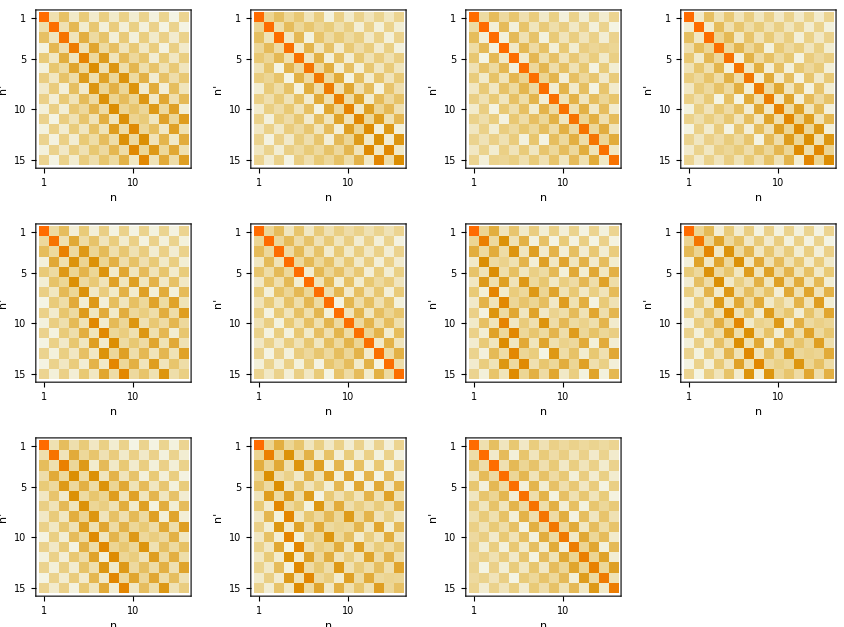

```mathematica
GraphicsGrid[{{MatrixPlot[U21,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 1"},{"n'",""}}],MatrixPlot[U23,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 3"},{"n'",""}}],MatrixPlot[U35,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 5"},{"n'",""}}],MatrixPlot[U41,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","4 -> 1"},{"n'",""}}]},{MatrixPlot[U64,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 4"},{"n'",""}}],MatrixPlot[U51,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","5 -> 1"},{"n'",""}}],MatrixPlot[U65,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 5"},{"n'",""}}],MatrixPlot[U75,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","7 -> 5"},{"n'",""}}]},{MatrixPlot[U27,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 7"},{"n'",""}}],MatrixPlot[U26,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 6"},{"n'",""}}],MatrixPlot[U34,FrameLabel -> {{"n","3 -> 4"},{"n'",""}}]}}]
```

```mathematica
Total[U41[[All,10]]]
```

1.02743182131628409

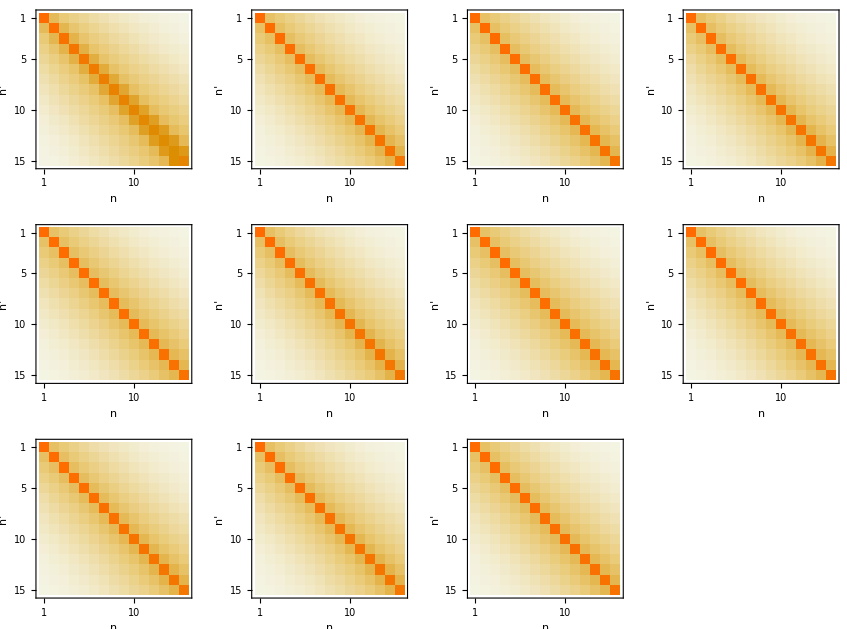

```mathematica
GraphicsGrid[{{MatrixPlot[D12,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","1 -> 2"},{"n'",""}}],MatrixPlot[D23,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 3"},{"n'",""}}],MatrixPlot[D35,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 5"},{"n'",""}}],MatrixPlot[D41,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","4 -> 1"},{"n'",""}}]},{MatrixPlot[D64,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 4"},{"n'",""}}],MatrixPlot[D51,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","5 -> 1"},{"n'",""}}],MatrixPlot[D65,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","6 -> 5"},{"n'",""}}],MatrixPlot[D75,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","7 -> 5"},{"n'",""}}]},{MatrixPlot[D27,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 7"},{"n'",""}}],MatrixPlot[D26,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","2 -> 6"},{"n'",""}}],MatrixPlot[D34,ColorFunctionScaling->True,PlotRange->{0,1},FrameLabel -> {{"n","3 -> 4"},{"n'",""}}]}}]
```

```mathematica
PathTot = 0.201004/(0.2001004+0.3678+0.25827)*PathA +0.3678/(0.2001004+0.3678+0.25827) PathB + 0.25827/(0.2001004+0.3678+0.25827) PathF;
PathTotE = 0.201004/(0.2001004+0.3678+0.25827+0.154494)*PathA +0.3678/(0.2001004+0.3678+0.25827+0.154494) PathB + 0.25827/(0.2001004+0.3678+0.25827+0.154494) PathF + 0.154494/(0.2001004+0.3678+0.25827 +0.154494)PathE;
(*+ +0.001969 PathC +0.016289PathD + 0.154494PathE ;*)
Paths ={PathA, PathB, PathC, PathD, PathE, PathF, PathTotE, PathTot, PathR};
```

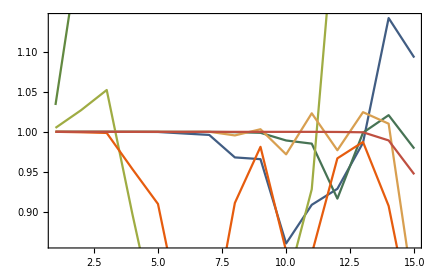

```mathematica
Show[{ListPlot[Table[Total[Table[Abs[PathA[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][1/8], Joined -> True, PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathB[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][2/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathC[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][3/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathD[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> ColorData["DarkRainbow"][4/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathE[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"]}[5/8],Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],ListPlot[Table[Total[Table[Abs[PathF[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"][6/8]},Joined -> True,PlotTheme -> "Scientific",PlotRange-> All],
ListPlot[Table[Total[Table[Abs[PathR[[l,j+1]]],{j,0,nmax}]],{l,1,nmax+1}],PlotStyle -> {ColorData["DarkRainbow"][7/8]},Joined -> True,PlotTheme -> "Scientific",PlotRange-> All]
}]
```

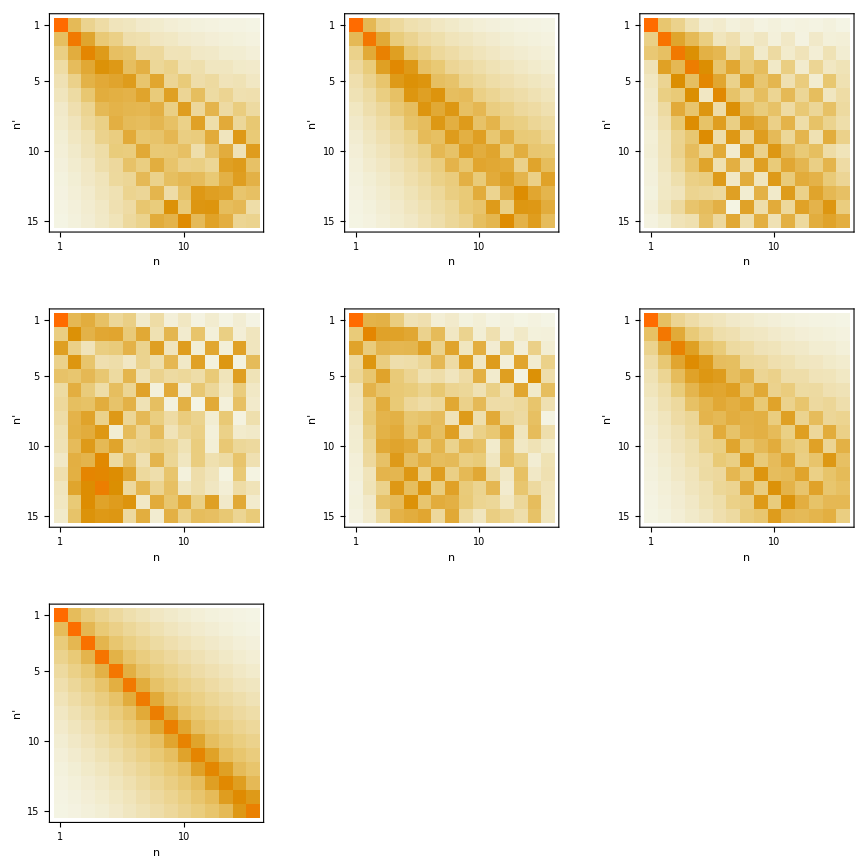

```mathematica
GraphicsGrid[{{MatrixPlot[PathA,FrameLabel -> {{"n","Path A: 2 -> 3 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],
MatrixPlot[PathB,FrameLabel -> {{"n","Path B: 2 -> 3 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],
MatrixPlot[PathC,FrameLabel -> {{"n","Path C: 2 -> 6 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}]
},
{MatrixPlot[PathD,FrameLabel -> {{"n","Path D: 2 -> 6 -> 4 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}],
MatrixPlot[PathE,FrameLabel -> {{"n","Path E: 2 -> 7 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black ,ColorFunctionScaling->True,PlotRange->{0,1}],
MatrixPlot[PathF,FrameLabel -> {{"n","Path F: 2 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ]},{MatrixPlot[PathR,FrameLabel -> {{"n","Path Red Imaging: 1 -> 5 -> 1"},{"n'",""}},FrameStyle-> Black,ColorFunctionScaling->True,PlotRange->{0,1} ],None,None}}, FrameStyle-> Black]
```

```mathematica
Total[PathE[[2]]]
```

0.999487953043637596

```mathematica
tablePath[pa_]:=Table[Sum[Paths[[pa]][[r,All]][[ra]] ra,{ra,1,nmax+1}],{r,1,Length[Paths[[pa]][[1,All]]]}]
tablePath[6]
tablePath[1]
tablePath[2]
tablePath[5]
```

{1.15362489518389578,2.27275539995127837,3.3893510729043618,4.50337449580959716,5.61474718976027274,6.71826186588065439,7.81796604045682439,8.79764020426292144,9.85961280101159448,10.066280850233751,11.1797911139021564,10.3155699461096624,11.1834167512955842,11.2858003072622739,9.0368229105704462}

{1.19176550319117698,2.37036683720270213,3.54626831693516549,4.71894713683413625,5.88736453810822543,7.02399016212159802,8.1393995257890859,8.83696137211941854,9.73362659845182543,9.06733041600137996,10.0840810967912374,10.6650478771523343,11.2681480644610778,12.1903520095755959,11.4578687091959497}

{1.12534306854060459,2.16353934023568145,3.20075718625274224,4.23701133607697747,5.27231327652822693,6.30660310240988723,7.33956894267070258,8.36571088187685022,9.3795509703665261,10.246397201928999,11.1126534551219888,10.9483084360555419,12.5220174058140963,12.9958331253038601,12.2630019260402173}

{1.77060326445567816,4.01959805002683202,6.16215694428531423,7.33590697723583406,7.94048936283689505,6.02533132161662224,5.61762916986945317,6.92987293996839029,7.54008766300718434,5.66896870938462883,5.95183061938191543,7.01601137505887035,7.24208587973784973,6.69799166161738758,5.79386563492988593}

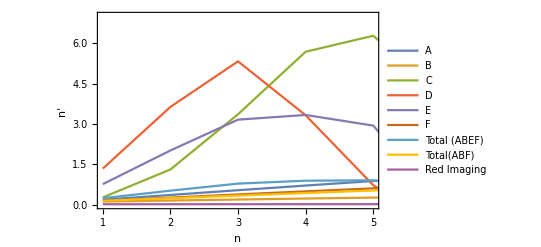

```mathematica
heatdata=Table[Table[Sum[Paths[[pa]][[r]][[ra]] ra,{ra,1,nmax+1}]-r,{r,1,Length[Paths[[pa]][[1,All]]]}],{pa,1,9}];
ListPlot[heatdata,PlotStyle -> ColorData["DarkRainbow"][pa/9],Joined -> True,FrameStyle -> Black, Frame -> True,PlotRange-> {{1,5},{0,7}}, FrameLabel->{"n", "n'"}, PlotLegends-> {"A","B","C","D","E","F","Total (ABEF)","Total(ABF)","Red Imaging"}]
```

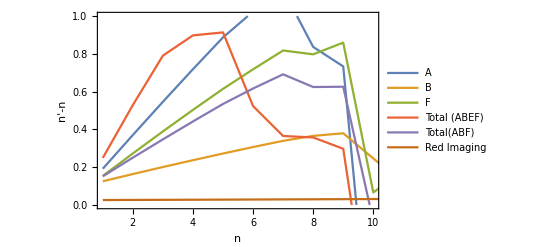

```mathematica
heatdata=Table[Table[Sum[Paths[[pa]][[r]][[ra]] ra,{ra,1,nmax+1}]-r,{r,1,Length[Paths[[pa]][[1,All]]]}],{pa,{1,2,6,7,8,9}}];
ListPlot[heatdata,PlotStyle -> ColorData["DarkRainbow"][pa/9],Joined -> True,FrameStyle -> Black, Frame -> True,PlotRange-> {{1,10},{0,1}}, FrameLabel->{"n", "n'-n"}, PlotLegends-> { "A","B","F","Total (ABEF)","Total(ABF)","Red Imaging"}]
```

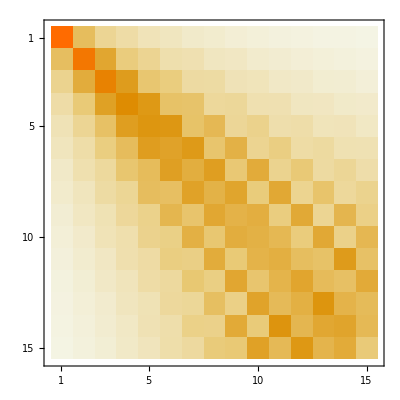

```mathematica
MatrixPlot[PathTot]
```

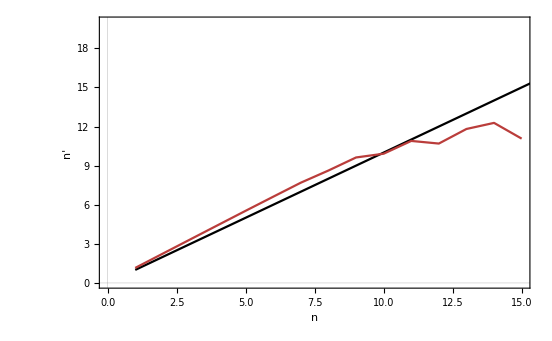

```mathematica
Show[{Plot[x,{x,1,50}, PlotStyle -> Directive[Black], PlotTheme -> "Scientific"],Table[plotPath[p],{p,7,7}]},PlotRange -> {{0,15},{0,20}}, FrameLabel->{"n", "n'"}, FrameStyle -> Black]
```

```mathematica
[0.16124798621448377,0.0960334115732626,0.0332789066157976,0.0016231605579470716,0.013017843524480264,0.06493276951481868,0.14643169575376094,0.2441025496108808,0.3457443802069478,0.4417818142898974,0.5251457579923736,0.5903808136735292,0.6325476768974604,0.6463973745099829,0.6264258662807234]
```

Multi-Experimente

```mathematica
intensities = Import["intensities.csv","csv"];
```

```mathematica
heatings = Import["heatings.csv", "csv"];
```

```mathematica
totheating = PathTot = 0.201004/(0.2001004+0.3678+0.25827)*PathA +0.3678/(0.2001004+0.3678+0.25827) PathB + 0.25827/(0.2001004+0.3678+0.25827) PathF;
PathTotE = 0.201004/(0.2001004+0.3678+0.25827+0.154494)*PathA +0.3678/(0.2001004+0.3678+0.25827+0.154494) PathB + 0.25827/(0.2001004+0.3678+0.25827+0.154494) PathF + 0.154494/(0.2001004+0.3678+0.25827 +0.154494)PathE;
```

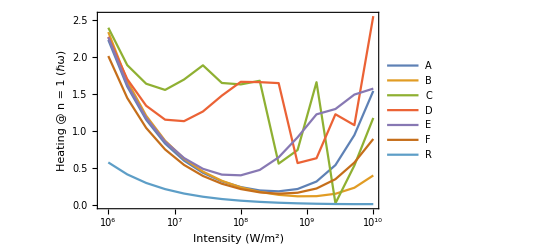

```mathematica
ListLogLinearPlot[Table[Thread[{Flatten[intensities], heatings[[All,in]]}],{in,1,7}], Joined -> True, PlotLegends-> {"A","B","C","D","E","F","R"}, Frame -> True, FrameStyle-> Black, FrameLabel -> {"Intensity (W/m^2)","Heating @ n = 1 (ℏω)"}]
```

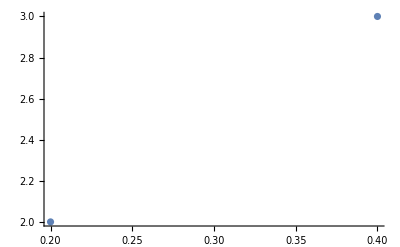

```mathematica
ListPlot[{{0.2,2},{0.4,3}}]
```